# Introdução à Física Computacional I (2023.2)

## Aula 8: importação de dados; ajustes não lineares

## Importando dados

Ao trabalharmos com dados experimentais, muitas vezes queremos ler esses dados de um arquivo (gerado, por exemplo, por um equipamento) em vez de digitá-los diretamente no Mathematica. Isso pode ser feito com a função Import.

Antes de exemplificá-la, vale destacar que é útil conhecer as funções SetDirectory e NotebookDirectory. A primeira define a pasta de trabalho e a segunda retorna a pasta em que o notebook atual está salvo. Vamos supor aqui que os arquivos a importar estejam localizados na mesma pasta que o notebook:

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\marco\OneDrive\Ambiente de Trabalho\Wolfram Mathematica\Aulas

Note que invocamos a função NotebookDirectory com um argumento vazio, o que é entendido como uma referência ao notebook atual.

O problema que investigaremos hoje diz respeito a oscilações de um tablet, capturadas por um aplicativo que faz uso do acelerômetro do próprio aparelho. O vídeo que mostra esse movimento está disponível na pasta do notebook, sob o nome de “videosem.mp4”. Vamos importá-lo com a função Import:

```mathematica
Import["videosem.mp4"]
```

Note que a função identifica o tipo de arquivo por sua extensão (aqui, “.mp4”). Veja a documentação para mais informações.

Também na pasta do notebook há um arquivo, chamado “dadossem.dat”, contendo duas colunas com os dados de tempo e de posição (em relação ao equilíbrio). Para importá-lo, fazemos novamente uso de Import. Em seguida, vamos fazer o gráfico dos dados (que são importados como uma lista).
Ou seja, qundo quiser plotar alguma coisa coloque os dados em um bloco de notas com os dados de x e y.

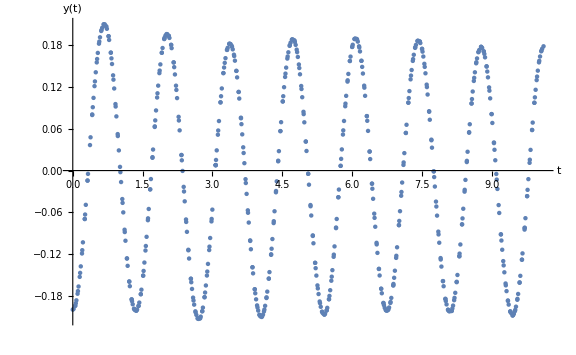

```mathematica
dadossem=Import["dadossem.dat"]; 
optam={ImageSize->Large,LabelStyle-> Large};
grafsem=ListPlot[dadossem,Evaluate[optam],AxesLabel->{"t","y(t)"}]
```

O movimento parece periódico, com pequenas discrepâncias que podem ser atribuídas ao fato de que a trajetória do tablet não é perfeitamente unidimensional.

Vamos tentar ajustar o movimento àquele de um oscilador harmônico simples, utilizando a solução geral A cos(ω_0 t+ϕ) e encontrando os valores das constantes A, ω_0 e ϕ que melhor reproduzem os dados. Isso pode ser feito com o auxílio da função FindFit. (A função Fit, que discutimos anteriormente, somente trabalha com combinações lineares de funções que especificamos, ou seja, as constantes a ajustar somente podem multiplicar funções da “base” de ajuste.) É preciso dar bons palpites iniciais sobre os parâmetros, uma vez que o algoritmo de ajuste funciona pela minimização local dos erros. Nossos palpites serão A=-0.2, ω_0=2π/T com T estimado dos dados como 8.1/6, e ϕ=0. A sintaxe de FindFit é ilustrada abaixo:

```mathematica
parsem=FindFit[dadossem,A*Cos[ω0*t+ϕ],{{A, -0.2},{ω0,2*π/(8.1/6)},{ϕ, 0}},t]
```

{A→-0.197828,ω0→4.65387,ϕ→-0.00979076}

Vamos fazer um gráfico da função de ajuste com os dados obtidos a partir do uso de FindFit:

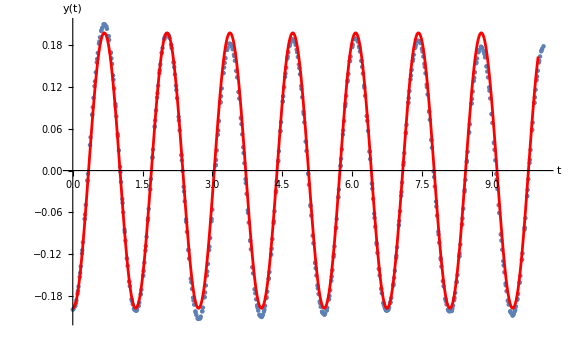

```mathematica
ajustesem=Plot[A*Cos[ω0*t+ϕ]/.parsem,{t,0,10},PlotStyle->Red]; 
Show[{grafsem,ajustesem}]
```

Agora vamos analisar o que ocorre quando colocamos um pedaço de papelão preso perpendicularmente ao tablet, de modo a produzir uma resistência do ar relevante.

```mathematica
Import["videocom.mp4"]
```

```mathematica
dadoscom=Import["dadoscom.dat"];
```

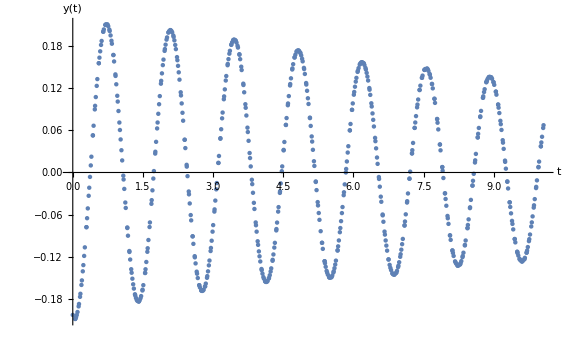

```mathematica
grafcom=ListPlot[dadoscom,Evaluate[optam],AxesLabel->{"t","y(t)"}]
```

Vamos tentar modelar o movimento sob resistência do ar, supondo que se trate de um atrito viscoso, descrito pela equação diferencial (d^2 x)/(d t^2)+γ(d x)/(d t)+ω_0^2 x=0, 
em que escrevemos x em vez de y para não induzir confusão com o parâmetro γ. Como vemos do gráfico que o atrito é pequeno, podemos impor a condição γ<ω_0/2 para evidenciar a presença de oscilações na solução.

```mathematica
eq=x''[t]+γ*x'[t]+ω0^2*x[t]==0;
Assuming[{ω0>0,γ>0,γ<ω0/2},DSolve[eq,x[t],t]//FullSimplify]
```

{{x[t]→ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ω0^2))) (C[1]+ⅇ^(ⅈ t √(-γ^2+4 ω0^2)) C[2])}}

Da saída da função DSolve, temos uma solução da forma x(t)=A e^(-γ t/2)cos(ω t+ϕ), com ω^2=ω_0^2-γ^2/4. No próximo slide, vamos buscar um ajuste dos dados a partir dessa forma.

```mathematica
xcom=A*Exp[-γ*t/2]*Cos[ω*t+ϕ]/.{ω-> Sqrt[ω0^2-γ^2/4]};
parcom=FindFit[dadoscom,xcom,{{A, -0.2},{ω0,2*π/(8.1/6)},{ϕ, 0},{γ,0.01}},t]
```

{A→-0.210726,ω0→4.59735,ϕ→-0.175503,γ→0.1038}

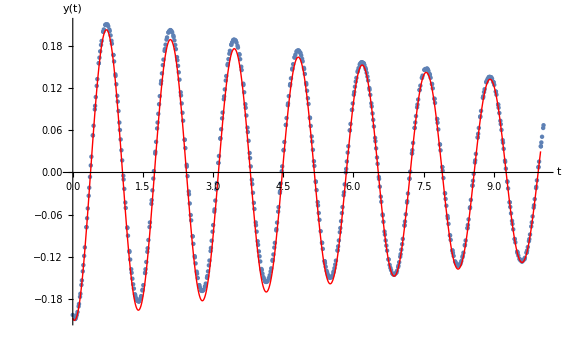

```mathematica
ajustecom=Plot[xcom/.parcom,{t,0,10},PlotStyle->{Red,Thick}]; 
Show[{grafcom,ajustecom}]
```

Vamos comparar os valores de ω_0 extraídos a partir dos dados com e sem atrito relevante:

```mathematica
Print[ω0/.parcom,"  ",ω0/.parsem]
```

4.59735  4.65387

Os valores parecem bastante próximos, mas para afirmar que são compatíveis precisamos conhecer as estimativas de erros desses valores segundo os ajustes. Para isso, precisamos executar os ajustes não com a função FindFit, mas sim com a função NonlinearModelFit, que armazena um conjunto maior de informações. A saída dessa função tem uma série de “propriedades” que armazenam as informações, e cuja leitura vamos exemplificar abaixo.

Primeiro examinamos os dados sem atrito:

```mathematica
nlmsem=NonlinearModelFit[dadossem,A*Cos[ω0*t+ϕ],{{A, -0.2},{ω0,2*π/(8.1/6)},{ϕ, 0}},t]; (*retorno os parâmetros*)
nlmsem["BestFitParameters"] (* Retorna as estimativas para os parâmetros *)
nlmsem["ParameterErrors"] (* Retorna os erros estimados para os parâmetros *)
nlmsem["AdjustedRSquared"] (* Retorna a estimativa de qualidade do ajuste, igual a 1 para um ajuste perfeito *)
```

{A→-0.197828,ω0→4.65387,ϕ→-0.00979076}

{0.000613934,0.00106601,0.00625094}

0.993872

Observe que os parâmetros do ajuste são os mesmos de antes, mas agora podemos visualizar os erros lendo a propriedade “ParameterErrors”.

Agora vamos examinar os dados com atrito:

```mathematica
nlmcom=NonlinearModelFit[dadoscom,xcom,{{A, -0.2},{ω0,2*π/(8.1/6)},{ϕ, 0},{γ,0.01}},t]; 
nlmcom["BestFitParameters"]
nlmcom["ParameterErrors"]
nlmcom["AdjustedRSquared"]
```

{A→-0.210726,ω0→4.59735,ϕ→-0.175503,γ→0.1038}

{0.00116833,0.00110144,0.005622,0.0022258}

0.99377

Ambas as estimativas de erro para ω_0 são muito menores do que a diferença entre as estimativas para o próprio ω_0. Isso sugere que nosso modelo pode ser melhorado!

Vamos então investigar um modelo que envolve um atrito proporcional ao quadrado da velocidade. A equação diferencial agora é (d^2 x)/(d t^2)+ρ(d x)/(d t)|(d x)/(d t)|+ω_0^2 x=0, que deve ser resolvida numericamente. No entanto, queremos poder ajustar os parâmetros ρ e ω_0, além da posição e da velocidade iniciais, o que implica variar seus valores. Para isso, é preciso resolver a equação diferencial com a função ParametricNDSolve:

```mathematica
eq2=x''[t]+ρ*x'[t]*Abs[x'[t]]+ω0^2*x[t]==0; sol2=ParametricNDSolve[{eq2,x[0]==x0,x'[0]==v0},x,{t,0,11},{ρ,x0,v0,ω0}] (* Podemos invocar a solução como x[ρ,x0,v0,ω0][t] *)
```

A solução paramétrica acima pode ser invocada com a sintaxe x[ρ,x0,v0,ω0][t]/.sol2:

```mathematica
Plot[x[0,1,0,2*π][t]/.sol2,{t,0,10},Evaluate[optam]]
```

Efetuamos agora o ajuste:

```mathematica
parcom2=FindFit[dadoscom,x[ρ,x0,v0,ω0][t]/.sol2,{{ρ,0.2},{x0, -0.2},{v0,0},{ω0,2*π/(8.1/6)}},t]
```

Fazemos o gráfico da função de ajuste com os parâmetros obtidos e comparamos com os resultados obtidos supondo atrito linear na velocidade:

```mathematica
ajustecom2=Plot[x[ρ,x0,v0,ω0][t]/.sol2/.parcom2,{t,0,10},PlotStyle->{Green,Dashed,Thick}]; 
figura=Show[{grafcom,ajustecom,ajustecom2}]
```

Na prática não há diferença entre os gráficos obtidos para atrito viscoso e para arraste. Isso decorre do fato de que, em ambos os casos, o atrito é muito pequeno.

```mathematica
nlmcom2=NonlinearModelFit[dadoscom,x[ρ,x0,v0,ω0][t]/.sol2,{{ρ,0.2},{x0, -0.2},{v0,0},{ω0,2*π/(8.1/6)}},t]; 
nlmcom2["BestFitParameters"]
nlmcom2["ParameterErrors"]
nlmcom2["AdjustedRSquared"]
```

Note que os valores de ω_0 previstos por ambos os tipos de atrito são compatíveis entre si, dados os erros, e que as estimativas da qualidade do ajuste também são muito semelhantes. No entanto, a literatura de dinâmica de fluidos sugere que a aproximação de atrito viscoso é inapropriada sempre que o número de Reynolds R_e do problema é muito maior do que 1. Esse número é definido como R_e=v L/ η, sendo v a velocidade do objeto, L sua escala de comprimento característica e η a viscosidade cinética do meio. Para o experimento que analisamos, podemos tomar v como a maior velocidade atingida pelo tablet (|ω_0 A|≃0.9 m/s), L como a raiz quadrada da área do pedaço de papelão (19 cm) e, para o ar, é conhecido que η=15×10^-6 m^2/s. Temos então R_e≃11000, o que indica que o atrito viscoso é, fundamentalmente, uma má aproximação.

Por que os valores de ω_0 previstos por ambos os modelos de atrito são compatíveis entre si mas incompatíveis com aquele previsto a partir dos dados sem atrito?

Lembre que ω_0=√(k/m), sendo k a constante elástica efetiva do sistema e m a massa do oscilador. O conjunto de molas é o mesmo nos dois casos, de modo que k não muda e concluímos que a massa é que deve ter mudado. Poderíamos pensar que a presença do papelão aumenta a massa, mas no experimento sem atrito o papelão já estava lá, apoiado na parte de trás do tablet e, portanto, oculto no primeiro vídeo.

No entanto, há uma massa “oculta” no problema sem atrito: a massa de ar deslocada pelo movimento do papelão. A área do papelão é de 360 cm^2, e seu deslocamento máximo é de cerca de 40 cm, de modo que o volume de ar deslocado é da ordem de 14000 cm^3. Como a densidade do ar é de cerca de 1.2×10^-3 g/cm^3, a massa total de ar deslocada é da ordem de 14 gramas, ou 4% da massa do tablet (356 g). A partir da razão entre os valores estimados de ω_0 sem e com atrito, sendo m_s e m_c as massas correspondentes, obtemos (m_c-m_s)/m_s=(4.65/4.60)^2-1, ou seja, a massa “adicional” corresponde a 2% da massa do tablet, da mesma ordem de grandeza da massa de ar deslocada.

Se quisermos exportar o último gráfico exibido (que atribuímos à variável figura), basta utilizarmos a função Export:

```mathematica
Export["ajustecom.png",figura]
```

Um arquivo de nome “ajustecom.png” deve ter sido criado na mesma pasta do notebook.

## Exercícios no E-disciplinas